#### define variables

```mathematica
xc = 0;
yc = 0;
ptc = {xc,yc};
ptmax = {xmax, ymax};
npts = 10;
ri = 1;
kg = 2.1;
rg = ri *kg;
sunnyshady = Sin[0.3x]Sin[0.5y];
initialcircle = CirclePoints[ri, 10];
```

#### define functions to use

```mathematica
funcSunnyShady[x_,y_]:=Sin[.3x]Sin[.5y]
```

```mathematica
findGradPoints[scalarFunc_,circlePoints_,x_,y_]:=Grad[scalarFunc[x,y],{x,y}]/.{x->circlePoints[[All,1]],y->circlePoints[[All,2]]}
```

#### find the gradient evaluated at points around circle (cartesian)

```mathematica
listPoints=findGradPoints[funcSunnyShady,initialcircle,x,y]
```

{{-0.136753,-0.084357,0.,0.084357,0.136753,0.136753,0.084357,0.,-0.084357,-0.136753},{0.0411508,0.115012,0.14776,0.115012,0.0411508,-0.0411508,-0.115012,-0.14776,-0.115012,-0.0411508}}

#### draw things

```mathematica
p0 = Graphics[initialcircle]
```

-Graphics-

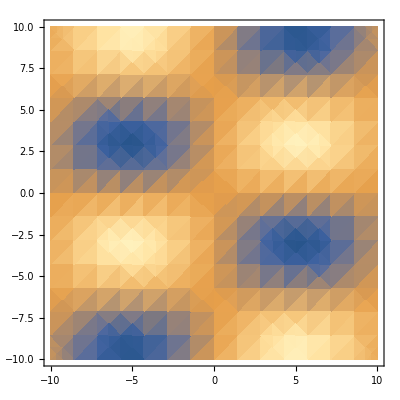

```mathematica
p1 = DensityPlot[Sin[0.3x]Sin[0.5y],{x,-10,10},{y,-10,10}]
```

```mathematica
Show[p1,p0]
```

-Graphics-